```mathematica
1+1
```

2

```mathematica
(*<<"C:\\Users\\fsiano\\work\\dev\\workspace\\optLNG\\optExhaustiveSearch\\Kernel\\optExhaustiveSearch.m"*)
```

## Input

All volumes in units of m^3
All charging/discharging rates in units of m^3/h
All boil-off rates in units of percentage/day

```mathematica
LNGTerminals=$terminalSpec;
LNGVessels=$vesselSpec;
```

```mathematica
GeoMarker[#["LatLong"]] & /@ LNGTerminals
```

```mathematica
GeoGraphics[GeoMarker[#["LatLong"]] & /@ LNGTerminals, GeoRange->All]
```

```mathematica
GeoGraphics[GeoMarker[#["Position"]] & /@ LNGVessels, GeoRange->All]
```

```mathematica
Dataset[LNGTerminals]
```

Dataset[<>]

```mathematica
Dataset[LNGVessels]
```

Dataset[<>]

```mathematica
GeoDistance[{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]},UnitSystem->"NauticalMiles"]/LNGVessels["WSD50"]["Speed"]
```

278.707 h

```mathematica
{LNGVessels["WSD50"]["Position"], LNGTerminals["Golden Pass"]["LatLong"]}
```

{GeoPosition[{58.97,5.71}],GeoPosition[{29.7616,-93.9292}]}

```mathematica
Tuples[Outer[{#1, #2, #3}&, Keys[LNGVessels], Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]], Keys[Select[LNGTerminals, #Type=="Import and Re-gasification" &]], 1, 1, 1]]
```

```mathematica
v={v1, v2, v3};
p={p1, p2, Missing[]};
m={m1, m2, m3};
```

```mathematica
Tuples[{v, p, m}]
```

{{v1,p1,m1},{v1,p1,m2},{v1,p1,m3},{v1,p2,m1},{v1,p2,m2},{v1,p2,m3},{v1,p3,m1},{v1,p3,m2},{v1,p3,m3},{v2,p1,m1},{v2,p1,m2},{v2,p1,m3},{v2,p2,m1},{v2,p2,m2},{v2,p2,m3},{v2,p3,m1},{v2,p3,m2},{v2,p3,m3},{v3,p1,m1},{v3,p1,m2},{v3,p1,m3},{v3,p2,m1},{v3,p2,m2},{v3,p2,m3},{v3,p3,m1},{v3,p3,m2},{v3,p3,m3}}

```mathematica
Tuples[{v, p}]/. {a_,b_}->a->b
```

{v1→p1,v1→p2,v1→p3,v2→p1,v2→p2,v2→p3,v3→p1,v3→p2,v3→p3}

```mathematica
Graph[Join[Tuples[{v, p}]/. {a_,b_}->a->b, Tuples[{p, m}]/. {a_,b_}->a->b], VertexLabels->"Name"]
```

```mathematica
FindPath[Out[34], v1, m1, Infinity, All]
```

{{v1,p3,m1},{v1,p2,m1},{v1,p1,m1}}

```mathematica
Permutations[v]
```

{{v1,v2,v3},{v1,v3,v2},{v2,v1,v3},{v2,v3,v1},{v3,v1,v2},{v3,v2,v1}}

```mathematica
Permutations[p]
```

{{p1,p2},{p2,p1}}

```mathematica
Permutations[m]
```

{{m1,m2,m3},{m1,m3,m2},{m2,m1,m3},{m2,m3,m1},{m3,m1,m2},{m3,m2,m1}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ]
```

{{{v1,p1},{v2,p2},{v3,}},{{v1,p1},{v2,},{v3,p2}},{{v1,p2},{v2,p1},{v3,}},{{v1,p2},{v2,},{v3,p1}},{{v1,},{v2,p1},{v3,p2}},{{v1,},{v2,p2},{v3,p1}}}

```mathematica
DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, DeleteDuplicates[Flatten[Outer[Sort[Transpose[{#1, #2}]]&, Permutations[v], Permutations[p], 1, 1],1 ] ], Permutations[m], 1, 1], 1]]
```

{{{{v1,p1},m1},{{v2,p2},m2},{{v3,Missing[]},m3}},{{{v1,p1},m1},{{v2,p2},m3},{{v3,Missing[]},m2}},{{{v1,p1},m2},{{v2,p2},m1},{{v3,Missing[]},m3}},{{{v1,p1},m2},{{v2,p2},m3},{{v3,Missing[]},m1}},{{{v1,p1},m3},{{v2,p2},m1},{{v3,Missing[]},m2}},{{{v1,p1},m3},{{v2,p2},m2},{{v3,Missing[]},m1}},{{{v1,p1},m1},{{v2,Missing[]},m2},{{v3,p2},m3}},{{{v1,p1},m1},{{v2,Missing[]},m3},{{v3,p2},m2}},{{{v1,p1},m2},{{v2,Missing[]},m1},{{v3,p2},m3}},{{{v1,p1},m2},{{v2,Missing[]},m3},{{v3,p2},m1}},{{{v1,p1},m3},{{v2,Missing[]},m1},{{v3,p2},m2}},{{{v1,p1},m3},{{v2,Missing[]},m2},{{v3,p2},m1}},{{{v1,p2},m1},{{v2,p1},m2},{{v3,Missing[]},m3}},{{{v1,p2},m1},{{v2,p1},m3},{{v3,Missing[]},m2}},{{{v1,p2},m2},{{v2,p1},m1},{{v3,Missing[]},m3}},{{{v1,p2},m2},{{v2,p1},m3},{{v3,Missing[]},m1}},{{{v1,p2},m3},{{v2,p1},m1},{{v3,Missing[]},m2}},{{{v1,p2},m3},{{v2,p1},m2},{{v3,Missing[]},m1}},{{{v1,p2},m1},{{v2,Missing[]},m2},{{v3,p1},m3}},{{{v1,p2},m1},{{v2,Missing[]},m3},{{v3,p1},m2}},{{{v1,p2},m2},{{v2,Missing[]},m1},{{v3,p1},m3}},{{{v1,p2},m2},{{v2,Missing[]},m3},{{v3,p1},m1}},{{{v1,p2},m3},{{v2,Missing[]},m1},{{v3,p1},m2}},{{{v1,p2},m3},{{v2,Missing[]},m2},{{v3,p1},m1}},{{{v1,Missing[]},m1},{{v2,p1},m2},{{v3,p2},m3}},{{{v1,Missing[]},m1},{{v2,p1},m3},{{v3,p2},m2}},{{{v1,Missing[]},m2},{{v2,p1},m1},{{v3,p2},m3}},{{{v1,Missing[]},m2},{{v2,p1},m3},{{v3,p2},m1}},{{{v1,Missing[]},m3},{{v2,p1},m1},{{v3,p2},m2}},{{{v1,Missing[]},m3},{{v2,p1},m2},{{v3,p2},m1}},{{{v1,Missing[]},m1},{{v2,p2},m2},{{v3,p1},m3}},{{{v1,Missing[]},m1},{{v2,p2},m3},{{v3,p1},m2}},{{{v1,Missing[]},m2},{{v2,p2},m1},{{v3,p1},m3}},{{{v1,Missing[]},m2},{{v2,p2},m3},{{v3,p1},m1}},{{{v1,Missing[]},m3},{{v2,p2},m1},{{v3,p1},m2}},{{{v1,Missing[]},m3},{{v2,p2},m2},{{v3,p1},m1}}}

```mathematica
(Sort/@Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&,Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&, Permutations[<|"Vessel"->#|> & /@v], Permutations[<|"Production"->#|> & /@p], 1, 1],1 ], Permutations[<|"Market"->#|> & /@m], 1, 1], 1])//DeleteDuplicates
```

{{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→p1,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→p1,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→p1,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m3|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→Missing[],Market→m2|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→Missing[],Market→m1|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→p2,Market→m1|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→p2,Market→m2|>,<|Vessel→v2,Production→Missing[],Market→m3|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m1|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→p2,Market→m3|>,<|Vessel→v2,Production→Missing[],Market→m2|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→p2,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p1,Market→m3|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p1,Market→m1|>,<|Vessel→v3,Production→p2,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p1,Market→m2|>,<|Vessel→v3,Production→p2,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m1|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→p1,Market→m3|>},{<|Vessel→v1,Production→Missing[],Market→m2|>,<|Vessel→v2,Production→p2,Market→m3|>,<|Vessel→v3,Production→p1,Market→m1|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p2,Market→m1|>,<|Vessel→v3,Production→p1,Market→m2|>},{<|Vessel→v1,Production→Missing[],Market→m3|>,<|Vessel→v2,Production→p2,Market→m2|>,<|Vessel→v3,Production→p1,Market→m1|>}}

### Connect to aquaplot

```mathematica
xxx=URLExecute[HTTPRequest["https://api.aquaplot.com/v1/quota", VerifySecurityCertificates->False]];
```

```mathematica
xxx
```

```mathematica
xxx=URLExecute["https://api.aquaplot.com/v1/quota"]
```

```mathematica
xxx
```

```mathematica
xxx=URLExecute[HTTPRequest["https://api.aquaplot.com/v1/route/from/32.67333984375/33.17434155100208/to/35.92529296875/24.806681353851964"]]
```

```mathematica
URLExecute["http://en.wikipedia.org/w/api.php",{"format"->"json","action"->"query","titles"->"Main Page","prop"->"revisions","rvprop"->"content"}]//Short
```

{batchcomplete→,query→{pages→{15580374→{pageid→15580374,«2»,revisions→{{contentformat→text/x-wiki,«1»,c…el→…}}}}}}

### Make a list of possible decisions

```mathematica
v=Normal[Keys[LNGVessels]];
p=Normal[Keys[Select[LNGTerminals, #Type=="Liquification and Export" &]]];
m=Normal[Keys[Select[LNGTerminals, #Type=="Import and Re-gasification"&]]];
```

```mathematica
{v, p, m}=Module[{len=Max[Length[#]& /@ {v, p, m}]},
PadRight[#, len, Missing[]] & /@ {v, p, m}
];
```

```mathematica
decisions=(Sort/@Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&,Flatten[Outer[(Apply[Join,#] &/@Transpose[{#1, #2}])&, Permutations[<|"Vessel"->#|> & /@v], Permutations[<|"Production"->#|> & /@p], 1, 1],1 ], Permutations[<|"Market"->#|> & /@m], 1, 1], 1])//DeleteDuplicates ;
```

```mathematica
Length /@ {v, p, m}
```

{4,4,4}

```mathematica
Binomial[288, 30]
```

47701230579106532933000886614512970393712

```mathematica
decisions//Dimensions
```

{288,4}

```mathematica
decisions[[5]]
```

{<|Vessel→Leissner,Production→Missing[],Market→Arun LNG Terminal and Plant Indonesia|>,<|Vessel→Tembek,Production→Missing[],Market→Rudong Jiangsu LNG Terminal China|>,<|Vessel→TGE,Production→PNG LNG Terminal Papua New Guinea,Market→Missing[]|>,<|Vessel→WSD50,Production→Golden Pass,Market→Gate LNG Terminal Netherland|>}

Cashflow one trip

```mathematica
cashflowTrip[#["Vessel"], #["Production"], #["Market"]] & /@ {decisions[[5, 1]]}
```

{<|Vessel→<|Speed→13. nmi/h,Capacity→75000 m^3,Maximum loading rate→1000 m^3/day,Maximum discharge rate→1000 m^3/day,Boil-off rate→0.15,Position→GeoPosition[{5.2234,97.083}],Inventory→0 m^3,DailyFixedCost→200 $|>,Production→Missing[],Market→<|LatLong→GeoPosition[{5.2234,97.083}],Currency→Rupiah,Type→Import and Re-gasification,Total Terminal Storage Capacity→635000 m^3,Price→6.2 $|>,cashflows→-3 319.68 $|>}

```mathematica
cashflowTrip[#["Vessel"], #["Production"], #["Market"]] & /@ {decisions[[5, 4]]}
```

{<|Vessel→<|Speed→15. nmi/h,Capacity→20000 m^3,Maximum loading rate→1250 m^3/day,Maximum discharge rate→1250 m^3/day,Boil-off rate→0.12,Position→GeoPosition[{51.9718,4.0755}],Inventory→0 m^3,DailyFixedCost→100 $|>,Production→<|LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→4.1 $|>,Market→<|LatLong→GeoPosition[{51.9718,4.0755}],Currency→EUR,Type→Import and Re-gasification,Total Terminal Storage Capacity→540000 m^3,Price→4. $|>,cashflows→13 043.14 $|>}

```mathematica
xxx=Module[{local=#, lV, lP, lM},
lV=LNGVessels[local["Vessel"]];
lP=If[local["Production"]===Missing[], Missing[], LNGTerminals[local["Production"]]];
lM=If[local["Market"]===Missing[], Missing[], LNGTerminals[local["Market"]]];
cashflowTrip[ lV, lP, lM]
] & /@ decisions[[5]];
```

```mathematica
xxx
```

{<|Vessel→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,Speed→13. nmi/h,Capacity→75000 m^3,Maximum loading rate→1000 m^3/day,Maximum discharge rate→1000 m^3/day,Boil-off rate→0.15,Position→GeoPosition[{5.2234,97.083}],Inventory→-optExhaustiveSearch`Private`loadingVolume$10224+0 m^3,DailyFixedCost→200 $|>,Production→Missing[],Market→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,LatLong→GeoPosition[{5.2234,97.083}],Currency→Rupiah,Type→Import and Re-gasification,Total Terminal Storage Capacity→635000 m^3,Price→6.2 $|>,cashflows→-3 319.68 $|>,<|Vessel→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,Capacity→216100 m^3,Maximum loading rate→2600 m^3/day,Maximum discharge rate→1300 m^3/day,Boil-off rate→0,Position→GeoPosition[{32.5292,121.428}],Speed→16.7 nmi/h,Inventory→-optExhaustiveSearch`Private`loadingVolume$10258+0 m^3,DailyFixedCost→250 $|>,Production→Missing[],Market→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,LatLong→GeoPosition[{32.5292,121.428}],Currency→Yuan Renminbi,Type→Import and Re-gasification,Total Terminal Storage Capacity→680000 m^3,Price→6.5 $|>,cashflows→-2 785.48 $|>,<|Vessel→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,Speed→16. nmi/h,Capacity→30000 m^3,Maximum loading rate→2000 m^3/day,Maximum discharge rate→2500 m^3/day,Boil-off rate→0.19,Position→GeoPosition[{58.97,5.71}],Inventory→0 m^3,DailyFixedCost→150 $|>,Production→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,LatLong→GeoPosition[{-9.33862,147.018}],Currency→Kina,Type→Liquification and Export,Total Terminal Storage Capacity→320000 m^3,Daily Production→2500 m^3/day,Inventory→320000 m^3,Price→3.9 $|>,Market→optExhaustiveSearch`Private`m,cashflows→-∞ $|>,<|Vessel→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,Speed→15. nmi/h,Capacity→20000 m^3,Maximum loading rate→1250 m^3/day,Maximum discharge rate→1250 m^3/day,Boil-off rate→0.12,Position→GeoPosition[{51.9718,4.0755}],Inventory→0 m^3,DailyFixedCost→100 $|>,Production→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,LatLong→GeoPosition[{29.7616,-93.9292}],Currency→USD,Type→Liquification and Export,Total Terminal Storage Capacity→350000 m^3,Daily Production→5000 m^3/day,Inventory→100000 m^3,Price→4.1 $|>,Market→<|Timestamp→Sun 1 Jan 2018 00:00:00GMT (Juliancalendar),Status→Idle,LatLong→GeoPosition[{51.9718,4.0755}],Currency→EUR,Type→Import and Re-gasification,Total Terminal Storage Capacity→540000 m^3,Price→4. $|>,cashflows→13 043.14 $|>}

```mathematica
Total[#["cashflows"] & /@ xxx]
```

-∞ $

```mathematica
xxx={#, cashflowPlan[#]} & /@ (Function[dec, DeleteCases[dec, _?( #["Production"]===Missing[] || #["Market"]===Missing[] &)]] /@ decisions);
```

```mathematica
SortBy[xxx,#[[2]]["cashflows"] &][[-1]]
```

{{<|Vessel→Tembek,Production→PNG LNG Terminal Papua New Guinea,Market→Rudong Jiangsu LNG Terminal China|>,<|Vessel→WSD50,Production→Golden Pass,Market→Gate LNG Terminal Netherland|>},<|cashflows→1.3489626707974088e6 $|>}

```mathematica
xxx = valuation[DateObject[{2018,1,1},TimeObject[{0,0,0}]], DateObject[{2019,1,1},TimeObject[{0,0,0}]]];
```

```mathematica
UnitConvert[xxx[[2, 1]]["Daily Production"],  ("Meters")^3 / "Hours"]
```

625/3 m^3/h

```mathematica
AssociationThread[xxx[[1]][[1;;30]], Clip[xxx[[2, 1]]["Inventory"] + Accumulate[UnitConvert[xxx[[2, 1]]["Daily Production"],  ("Meters")^3 / "Hours"]  Range[30] Quantity[1, "Hours" ]], {Quantity[0, ("Meters")^3],xxx[[2, 1]]["Total Terminal Storage Capacity"] }]]
```

<|Mon 1 Jan 2018 00:00:00GMT→300625/3 m^3,Mon 1 Jan 2018 01:00:00GMT→100625 m^3,Mon 1 Jan 2018 02:00:00GMT→101250 m^3,Mon 1 Jan 2018 03:00:00GMT→306250/3 m^3,Mon 1 Jan 2018 04:00:00GMT→103125 m^3,Mon 1 Jan 2018 05:00:00GMT→104375 m^3,Mon 1 Jan 2018 06:00:00GMT→317500/3 m^3,Mon 1 Jan 2018 07:00:00GMT→107500 m^3,Mon 1 Jan 2018 08:00:00GMT→109375 m^3,Mon 1 Jan 2018 09:00:00GMT→334375/3 m^3,Mon 1 Jan 2018 10:00:00GMT→113750 m^3,Mon 1 Jan 2018 11:00:00GMT→116250 m^3,Mon 1 Jan 2018 12:00:00GMT→356875/3 m^3,Mon 1 Jan 2018 13:00:00GMT→121875 m^3,Mon 1 Jan 2018 14:00:00GMT→125000 m^3,Mon 1 Jan 2018 15:00:00GMT→385000/3 m^3,Mon 1 Jan 2018 16:00:00GMT→131875 m^3,Mon 1 Jan 2018 17:00:00GMT→135625 m^3,Mon 1 Jan 2018 18:00:00GMT→418750/3 m^3,Mon 1 Jan 2018 19:00:00GMT→143750 m^3,Mon 1 Jan 2018 20:00:00GMT→148125 m^3,Mon 1 Jan 2018 21:00:00GMT→458125/3 m^3,Mon 1 Jan 2018 22:00:00GMT→157500 m^3,Mon 1 Jan 2018 23:00:00GMT→162500 m^3,Tue 2 Jan 2018 00:00:00GMT→503125/3 m^3,Tue 2 Jan 2018 01:00:00GMT→173125 m^3,Tue 2 Jan 2018 02:00:00GMT→178750 m^3,Tue 2 Jan 2018 03:00:00GMT→553750/3 m^3,Tue 2 Jan 2018 04:00:00GMT→190625 m^3,Tue 2 Jan 2018 05:00:00GMT→196875 m^3|>

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2018,1,1,22,0,0.},"Instant","Gregorian",0.],"Hours",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

<|Mon 1 Jan 2018 04:00:00GMT→300625/3 m^3,Mon 1 Jan 2018 05:00:00GMT→301250/3 m^3,Mon 1 Jan 2018 06:00:00GMT→100625 m^3,Mon 1 Jan 2018 07:00:00GMT→302500/3 m^3,Mon 1 Jan 2018 08:00:00GMT→303125/3 m^3,Mon 1 Jan 2018 09:00:00GMT→101250 m^3,Mon 1 Jan 2018 10:00:00GMT→304375/3 m^3,Mon 1 Jan 2018 11:00:00GMT→305000/3 m^3,Mon 1 Jan 2018 12:00:00GMT→101875 m^3,Mon 1 Jan 2018 13:00:00GMT→306250/3 m^3,Mon 1 Jan 2018 14:00:00GMT→306875/3 m^3,Mon 1 Jan 2018 15:00:00GMT→102500 m^3,Mon 1 Jan 2018 16:00:00GMT→308125/3 m^3,Mon 1 Jan 2018 17:00:00GMT→308750/3 m^3,Mon 1 Jan 2018 18:00:00GMT→103125 m^3,Mon 1 Jan 2018 19:00:00GMT→310000/3 m^3,Mon 1 Jan 2018 20:00:00GMT→310625/3 m^3,Mon 1 Jan 2018 21:00:00GMT→103750 m^3,Mon 1 Jan 2018 22:00:00GMT→311875/3 m^3|>

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2018,1,2,4,0,0.},"Instant","Gregorian",0.],"Days",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

<|Tue 2 Jan 2018 03:00:00GMT→105000 m^3|>

```mathematica
makeProductionInventory[DateObject[{2018,1,1,3,0,0.},"Instant","Gregorian",0.],DateObject[{2020, 1, 1}],"Years",Quantity[100000, ("Meters")^3],Quantity[5000, ("Meters")^3/("Days")],Quantity[540000, ("Meters")^3]]
```

<|Tue 1 Jan 2019 03:00:00GMT→540000 m^3,Wed 1 Jan 2020 03:00:00GMT→540000 m^3|>

```mathematica
ts=TimeSeries[Transpose[{DateRange[DateObject[{2016, 6, 1}], DateObject[{2018, 5, 1}],"Months"], Quantity[#, "USDollars" / "Meters"^3] & /@ RandomReal[{2.0, 5.0}, 24]}], ResamplingMethod->{"Interpolation", InterpolationOrder->0}, CalendarType->"Julian", TimeZone->"Europe/London"]
```

TimeSeries[…]

```mathematica
ts["DatePath"]
```

{{Wed 19 May 2016 01:00:00GMT (Juliancalendar),3.31908 $},{Fri 18 Jun 2016 01:00:00GMT (Juliancalendar),3.09338 $},{Mon 19 Jul 2016 01:00:00GMT (Juliancalendar),4.03712 $},{Thu 19 Aug 2016 01:00:00GMT (Juliancalendar),4.06649 $},{Sat 18 Sep 2016 01:00:00GMT (Juliancalendar),3.42409 $},{Tue 19 Oct 2016 00:00:00GMT (Juliancalendar),3.15726 $},{Thu 18 Nov 2016 00:00:00GMT (Juliancalendar),3.00625 $},{Sun 19 Dec 2016 00:00:00GMT (Juliancalendar),4.89616 $},{Wed 19 Jan 2017 00:00:00GMT (Juliancalendar),4.08167 $},{Wed 16 Feb 2017 00:00:00GMT (Juliancalendar),3.55281 $},{Sat 19 Mar 2017 01:00:00GMT (Juliancalendar),4.90334 $},{Mon 18 Apr 2017 01:00:00GMT (Juliancalendar),2.69858 $},{Thu 19 May 2017 01:00:00GMT (Juliancalendar),3.94555 $},{Sat 18 Jun 2017 01:00:00GMT (Juliancalendar),4.97491 $},{Tue 19 Jul 2017 01:00:00GMT (Juliancalendar),4.93368 $},{Fri 19 Aug 2017 01:00:00GMT (Juliancalendar),4.49474 $},{Sun 18 Sep 2017 01:00:00GMT (Juliancalendar),4.49545 $},{Wed 19 Oct 2017 00:00:00GMT (Juliancalendar),2.55987 $},{Fri 18 Nov 2017 00:00:00GMT (Juliancalendar),2.39998 $},{Mon 19 Dec 2017 00:00:00GMT (Juliancalendar),2.51104 $},{Thu 19 Jan 2018 00:00:00GMT (Juliancalendar),4.65051 $},{Thu 16 Feb 2018 00:00:00GMT (Juliancalendar),2.40881 $},{Sun 19 Mar 2018 01:00:00GMT (Juliancalendar),2.2961 $},{Tue 18 Apr 2018 01:00:00GMT (Juliancalendar),2.26256 $}}

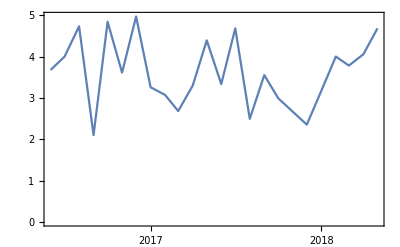

```mathematica
DateListPlot[%]
```

## Junk

### Define the region of all seas.

https://mathematica.stackexchange.com/questions/104407/geographics-path-within-a-country/104416#104416

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{51.9718, 4.0755}]}]
```

TravelDirections::noroute: Cannot compute path with travel method Driving between locations {GeoPosition[{29.7616,-93.9292}],GeoPosition[{51.9718,4.0755}]}.

$Failed

```mathematica
GeoGraphics[GeoMarker @ {GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.761564,-93.929215}]}]
```

```mathematica
TravelDirections[{GeoPosition[{29.761564,-93.929215}], GeoPosition[{39.76156,-93.929215}]}, TravelMethod->"Walking"]
```

TravelDirectionsData[…]

```mathematica
GeoGraphics[LinguisticAssistant]
```

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
Entity["Ocean","AtlanticOcean"]
```

Atlantic Ocean

```mathematica
allPonds=GeoGroup[{Entity["Ocean","AtlanticOcean"], Entity["Ocean","AdriaticSea"],Entity["Ocean","AegeanSea"],Entity["Ocean","AlboranSea"],Entity["Ocean","ArgentineSea"],Entity["Ocean","BayBiscay"],Entity["Ocean","BayBothnia"],Entity["Ocean","BayCampeche"],Entity["Ocean","BayFundy"],Entity["Ocean","BalticSea"],Entity["Ocean","BlackSea"],Entity["Ocean","BothnianSea"],Entity["Ocean","CaribbeanSea"],Entity["Ocean","CelticSea"],Entity["Ocean","CentralBalticSea"],Entity["Ocean","ChesapeakeBay"],Entity["Ocean","EnglishChannel"],Entity["Ocean","GulfBothnia"],Entity["Ocean","GulfGuinea"],Entity["Ocean","GulfFinland"],Entity["Ocean","GulfMexico"],Entity["Ocean","GulfSidra"],Entity["Ocean","GulfSaintLawrence"],Entity["Ocean","GulfVenezuela"],Entity["Ocean","IonianSea"],Entity["Ocean","LigurianSea"],Entity["Ocean","IrishSea"],Entity["Ocean","MarmaraSea"],Entity["Ocean","MediterraneanSea"],Entity["Ocean","MirtoonSea"],Entity["Ocean","NorthSea"],Entity["Ocean","SeaAzov"],Entity["Ocean","SeaCrete"],Entity["Ocean","SeaTheHebrides"],Entity["Ocean","SargassoSea"],Entity["Ocean","TampaBay"],Entity["Ocean","ThracianSea"],Entity["Ocean","TyrrhenianSea"],,}]
```

GeoGroup[{Atlantic Ocean,Adriatic Sea,Aegean Sea,Alboran Sea,Argentine Sea,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Baltic Sea,Black Sea,Bothnian Sea,Caribbean Sea,Celtic Sea,Central Baltic Sea,Chesapeake Bay,English Channel,Gulf of Bothnia,Gulf of Guinea,Gulf of Finland,Gulf of Mexico,Gulf of Sidra,Gulf of Saint Lawrence,Gulf of Venezuela,Ionian Sea,Ligurian Sea,Irish Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,North Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Sargasso Sea,Tampa Bay,Thracian Sea,Tyrrhenian Sea}]

```mathematica
poly=Entity["Ocean","AtlanticOcean"]["Polygon"]
```

Polygon[GeoPosition[…]]

```mathematica
pts=Flatten[poly[[1, 1]], 1];
```

```mathematica
line=Polygon[Range[##]]&@@@Partition[{1}~Join~Most[Riffle[Accumulate[Length/@#],1+Accumulate[Length/@#]]&@poly[[1,1]]],2];
```

```mathematica
aquifer=Quiet@DiscretizeRegion[MeshRegion[pts,line],MaxCellMeasure->.004];
```

```mathematica
GeoGraphics[aquifer]
```

```mathematica
allPonds=Cases[Union[Flatten[Join[EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","BorderingBodiesOfWater"]], EntityClass["Ocean","SevenSeas"][EntityProperty["Ocean","Basins"]]], 1]], Entity[___]]
```

{Adriatic Sea,Aegean Sea,Alboran Sea,Amundsen Gulf,Andaman Sea,Arabian Sea,Arafura Sea,Argentine Sea,Baffin Bay,Balearic Sea,Bali Sea,Baltic Sea,Banda Sea,Barents Sea,Bay of Bengal,Bay of Biscay,Bay of Bothnia,Bay of Campeche,Bay of Fundy,Beaufort Sea,Bering Sea,Bismarck Sea,Black Sea,Bohai Sea,Bohol Sea,Bothnian Sea,Cambridge Bay,Camotes Sea,Caribbean Sea,Celebes Sea,Celtic Sea,Central Baltic Sea,Ceram Sea,Chesapeake Bay,Chilean Sea,Chukchi Sea,Coastal Waters Of Southeast Alaska and British Columbia,Cold Bay,Coral Sea,Davis Strait,Denmark Strait,East China Sea,East Siberian Sea,English Channel,Flores Sea,Great Australian Bight,Greenland Sea,Gulf of Aden,Gulf of Alaska,Gulf of Bothnia,Gulf of California,Gulf of Carpentaria,Gulf of Finland,Gulf of Guinea,Gulf of Mexico,Gulf of Saint Lawrence,Gulf of Sidra,Gulf of Thailand,Gulf of Venezuela,Halmahera Sea,Hudson Bay,Indian Ocean,Inner Seas Off the West Coast of Scotland,Ionian Sea,Irish Sea,James Bay,Sea of Japan,Java Sea,Kara Sea,Kara Strait,Koro Sea,Labrador Sea,Laccadive Sea,Laptev Sea,Ligurian Sea,Lincoln Sea,Marmara Sea,Mediterranean Sea,Mirtoon Sea,Molucca Sea,Mozambique Channel,North Atlantic Ocean,North Pacific Ocean,North Sea,Northwest Passages,Norwegian Sea,Okhotsk Sea,Persian Gulf,Philippine Sea,Red Sea,Rio De La Plata,Salish Sea,Sargasso Sea,Savu Sea,Sea of Azov,Sea of Crete,Sea of Hebrides,Seto Inland Sea,Solomon Sea,South Atlantic Ocean,South China Sea,Southern Ocean,South Pacific Ocean,Strait of Gibraltar,Sulu Sea,Tampa Bay,Tasman Sea,Thracian Sea,Timor Sea,Tyrrhenian Sea,White Sea,Yellow Sea}